# Andre Lukas MM PS 1 - 3

We will use the symmetric Gaussian proposal distribution. Label the weight function w(x). Then, for first task, we wish to generate n points distributed according to w(x), meaning we can use Metropolis-Hastings algorithm to distribute our points. 

Proposal function Gaussian should be centred on the current point, using standard deviation 1 initially

```mathematica
ClearAll;

current = 0;
points = {current}; (*To form later list of points*)
w[x_] = Exp[-x^2];
n = 200000;
normalconst = Integrate[w[x], {x, -Infinity, Infinity}];

While[Length[points] < n,
sample = RandomVariate[NormalDistribution[current, 0.7]];
alpha = w[sample]/w[current];
rnd = RandomReal[];
If[rnd <= alpha, current = sample; AppendTo[points,sample], Null];]

points;
```

We can check the distribution of the points using a Histogram.

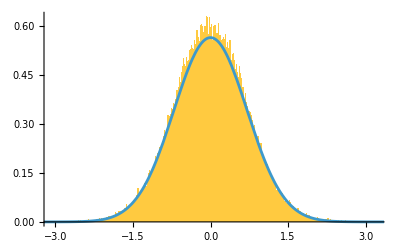

```mathematica
Show[Histogram[points, 1000, "PDF"],
Plot[w[x]/normalconst, {x, -5, 5}]]
```

Now, we want to use this to numerically integrate some function f(x) over the whole real line, using w(x) as a weight. We do so by comparing average values, which means normalising the weight function.

```mathematica
f[x_] = x^2;
exact = Integrate[f[x] * w[x], {x, -Infinity, Infinity}]/normalconst
approximate = 1/n * Sum[f[points[[i]]], {i, 1, n}]
```

1/2

0.47612